```mathematica
time = Quantity[1/(2 Pi),"PlanckConstant"]/Quantity[1,"Electronvolts"]
```

1/(2 π) h/eV

```mathematica
UnitSimplify[time]
```

44173801/(21362355120000000000000 π) s

```mathematica
QuantityMagnitude[Quantity[44173801/(21362355120000000000000 π),"Seconds"]]
```

44173801/(21362355120000000000000 π)

```mathematica
N[44173801/(21362355120000000000000 π)]
```

6.58212×10^-16

```mathematica
UnitSimplify[Quantity[2 Pi 0.0000018,("Electronvolts")/("PlanckConstant")]]
```

2.73468×10^9 Hz

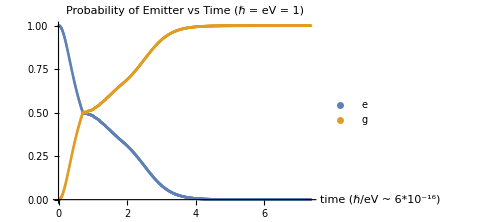

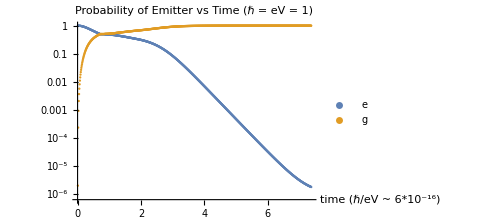

```mathematica
data = Import["/home/ethan/curr_proj/spaceData","Table"];
pUp = Table[{data[[j]][[1]],data[[j]][[2]]},{j,1,Length[data]-2}];
pDown = Table[{data[[j]][[1]],data[[j]][[3]]},{j,1,Length[data]-2}];
ListPlot[{pUp,pDown},PlotLabel->"Probability of Emitter vs Time (ℏ = eV = 1)",AxesLabel->{"time (ℏ/eV ~ 6*10^-16)"},PlotLegends->{"e","g"},ImageSize->Medium]
ListLogPlot[{pUp,pDown},PlotLabel->"Probability of Emitter vs Time (ℏ = eV = 1)",AxesLabel->{"time (ℏ/eV ~ 6*10^-16)"},PlotLegends->{"e","g"},ImageSize->Medium]
```

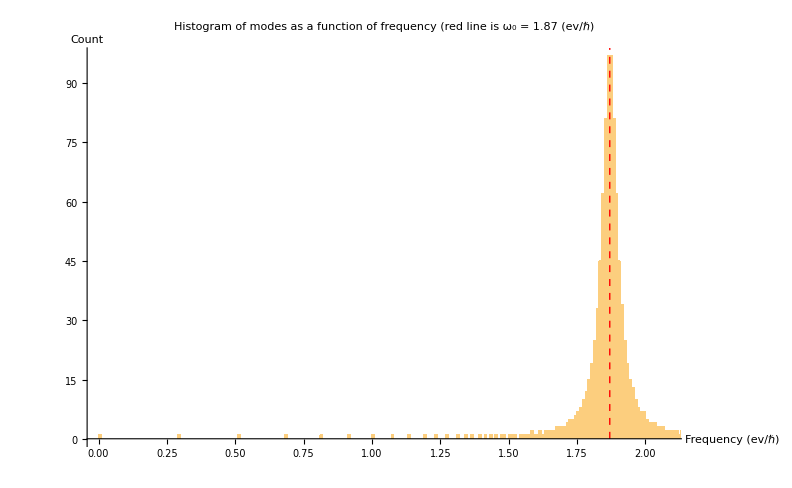

```mathematica
systemData = Import["/home/ethan/curr_proj/mode_and_couplings"];
histData = Table[systemData[[j]][[1]],{j,1,Length[systemData]}];
lineStyle={Red,Dashed};
lineOmega=Line[{{1.87,0},{1.87,100}}];
Histogram[histData,{.01},Epilog->{Directive[lineStyle],lineOmega},PlotLabel->"Histogram of modes as a function of frequency (red line is ω_0 = 1.87 (ev/ℏ)",AxesLabel->{"Frequency (ev/ℏ)","Count"}]
```

```mathematica
systemData = Import["/home/ethan/curr_proj/mode_and_couplings"];
lineStyle={Thin,Red,Dashed};
fgData = Table[{systemData[[j]][[1]],systemData[[j]][[2]]},{j,1,Length[systemData]}];
AppendTo[fgData,{1.87,.141}];
ListPlot[fgData,PlotLabel->"coupling as a function of frequency (red line is ω_0 = 1.87 (ev/ℏ)",AxesLabel->{"Frequency (ev/ℏ)","Coupling Strength"},Epilog->{Directive[lineStyle],lineOmega},PlotRange->Full]
```